# Import ToMatlab

```mathematica
Get["/Users/mallickrishg/Downloads/mathematica2matlab/mathematica2matlab/ToMatlab.m"]
```

# Corner Flow general solution

```mathematica
vx = -B-D*ArcTan[x,z] + (C*x + D*z)(-x/(x^2+z^2))
vz = A+C*ArcTan[x,z] + (C*x + D*z)(-z/(x^2+z^2))
edotxz = 0.5*(D[vx,z]+D[vz,x])//Simplify
edotxx = D[vx,x]//FullSimplify
edotzz = D[vz,z]//FullSimplify
edotxxdev = edotxx/2-edotzz/2//FullSimplify
```

-B-(x (C x+D z))/(x^2+z^2)-D ArcTan[x,z]

A-(z (C x+D z))/(x^2+z^2)+C ArcTan[x,z]

(-1. D x^3+1. C x^2 z+1. D x z^2-1. C z^3)/((x^2+z^2)^2)

(2 x z (D x-C z))/((x^2+z^2)^2)

(2 x z (-D x+C z))/((x^2+z^2)^2)

(2 x z (D x-C z))/((x^2+z^2)^2)

## Specify dip angle of subduction zone

```mathematica
δval = 25*Pi/180;
```

# Apply boundary conditions for continental arc corner flow

```mathematica
eq1 = ReplaceAll[vx,{ArcTan[x,z]->0,z->0}];
eq2 = ReplaceAll[vz,{ArcTan[x,z]->0,z->0}];
eq3=ReplaceAll[vx,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}];
eq4=ReplaceAll[vz,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}];
solarc =Solve[eq1==0&&eq2==0&&eq3==Cos[δ]&&eq4==-Sin[δ],{A,B,C,D},Reals,Assumptions->{δ>0,δ<Pi/2}]
```

{{A→0,B→-(2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),C→(2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),D→(2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2)+(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2))/(2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ])}}

```mathematica
solplot=ReplaceAll[solarc,{δ->δval}];
Aval=A/.solplot[[1]]
Bval=B/.solplot[[1]]//FullSimplify
Cval=C/.solplot[[1]]//FullSimplify
Dval=D/.solplot[[1]]//FullSimplify
```

0

-(180 π Sin[(5 π)/36])/(25 π^2+648 (-1+Sin[(2 π)/9]))

(180 π Sin[(5 π)/36])/(25 π^2+648 (-1+Sin[(2 π)/9]))

(36 (5 π Cos[(5 π)/36]-36 Sin[(5 π)/36]))/(25 π^2+648 (-1+Sin[(2 π)/9]))

# Plot velocity field

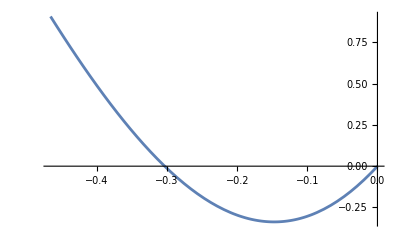

```mathematica
toplotxc=ReplaceAll[vx,{A->Aval,B->Bval,C->Cval,D->Dval}];
toplotzc=ReplaceAll[vz,{A->Aval,B->Bval,C->Cval,D->Dval}];
Rotate[Plot[ReplaceAll[toplotxc,{x->1}],{z,-1*Tan[δval],0}],Pi/2]
(*D[toplotx,z]+D[toplotz,x]//FullSimplify*)
```

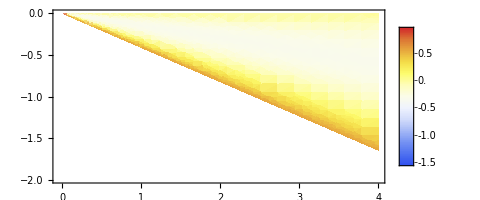

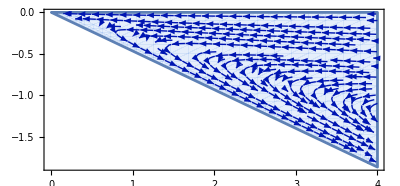

```mathematica
DensityPlot[toplotxc,{x,-0.04,4},{z,-2,0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},0>=Tan[z/x]>=-δval],AspectRatio->Automatic]
(*RegionFunction->Function[{x,z},0>=Tan[z/x]>=-δval]*)
p1=StreamPlot[{toplotxc,toplotzc},{x,-0.01,4},{z,-4*Tan[δval],0},RegionFunction->Function[{x,z},z+Tan[δval]*x>=0 && x>=0.0],StreamPoints->Fine,StreamScale->Tiny,AspectRatio->Automatic]
```

# Insert boundary conditions for oceanic mantle

```mathematica
eq1 = ReplaceAll[vx,{ArcTan[x,z]->-π,z->0}];
eq2 = ReplaceAll[vz,{ArcTan[x,z]->-π,z->0}];
eq3=ReplaceAll[vx,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}];
eq4=ReplaceAll[vz,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}];
solocean =Solve[eq1==1&&eq2==0&&eq3==Cos[δ]&&eq4==-Sin[δ],{A,B,C,D},Reals,Assumptions->{δ>0,δ<Pi/2}]
```

{{A→(π (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2),B→-1-(2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ])/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)+(π (2 Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)-(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)))/(2 π Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ]),C→(2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ])/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2),D→(2 Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)-(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2))/(2 π Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ])}}

```mathematica
solplot=ReplaceAll[solocean,{δ->δval}];
Aval=A/.solplot[[1]]
Bval=B/.solplot[[1]]//FullSimplify
Cval=C/.solplot[[1]]//FullSimplify
Dval=D/.solplot[[1]]//FullSimplify
```

(π (2-2 Cos[(5 π)/36]-31/9 π Sin[(5 π)/36]+2 Cos[(2 π)/9] Sin[(5 π)/36]-2 Sin[(2 π)/9]+2 Cos[(5 π)/36] Sin[(2 π)/9]))/(-1+(961 π^2)/324-Cos[(2 π)/9]^2+2 Sin[(2 π)/9]-Sin[(2 π)/9]^2)

(π (31 π (5-36 Cos[(5 π)/36])+36 (18 Cos[(2 π)/9]-5 Sin[(5 π)/36])))/(961 π^2+648 (-1+Sin[(2 π)/9]))

(36 Sin[(5 π)/36] (-31 π+36 Sin[(5 π)/36]))/(961 π^2+648 (-1+Sin[(2 π)/9]))

(72 Sin[(5 π)/72]^2 (31 π-36 Sin[(5 π)/36]))/(961 π^2+648 (-1+Sin[(2 π)/9]))

# Plot velocity field

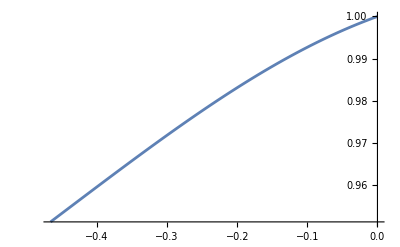

```mathematica
toplotxo=ReplaceAll[vx,{A->Aval,B->Bval,C->Cval,D->Dval}];
toplotzo=ReplaceAll[vz,{A->Aval,B->Bval,C->Cval,D->Dval}];
Rotate[Plot[ReplaceAll[toplotxo,{x->-1}],{z,-1*Tan[δval],0}],Pi/2]
```

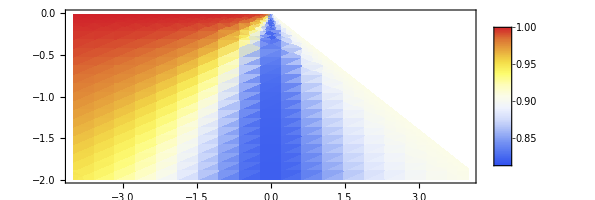

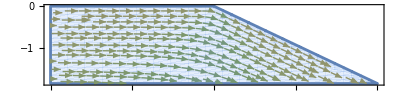

```mathematica
DensityPlot[toplotxo,{x,-4,4},{z,-2,0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},z+Tan[δval]*x<=0],AspectRatio->Automatic]
p2=StreamPlot[{toplotxo,toplotzo},{x,-4,4},{z,-4*Tan[δval],0},StreamPoints->Fine,StreamScale->Tiny,AspectRatio->Automatic,RegionFunction->Function[{x,z},z+Tan[δval]*x<=0 ],StreamColorFunction->"ArmyColors"]
```

# Show oceanic and continental corner flow

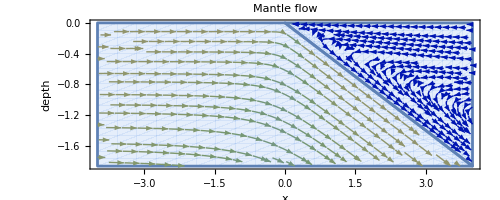

```mathematica
Show[p1,p2,PlotRange->All,AspectRatio->Automatic,ImageSize->500,PlotLabel->"Mantle flow",FrameLabel->{"x","depth"},BaseStyle->{FontSize->16}]
```

# Calculate strain rates from velocity

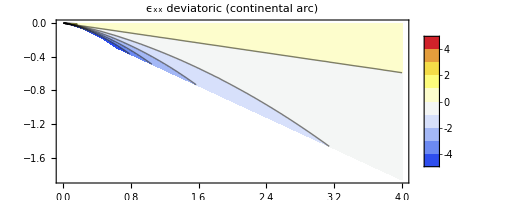

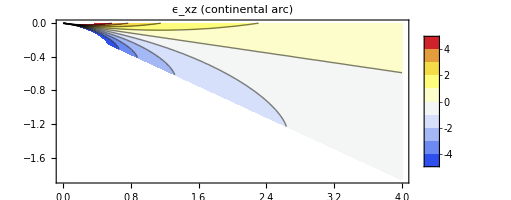

```mathematica
solplot=ReplaceAll[solarc,{δ->δval}];
Aval=A/.solplot[[1]];
Bval=B/.solplot[[1]];
Cval=C/.solplot[[1]];
Dval=D/.solplot[[1]];
toplotxx=ReplaceAll[edotxxdev,{A->Aval,B->Bval,C->Cval,D->Dval}]//FullSimplify;
toplotxz=ReplaceAll[edotxz,{A->Aval,B->Bval,C->Cval,D->Dval}]//FullSimplify;
ContourPlot[toplotxx,{x,-4,4},{z,-4*Tan[δval],0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},z+Tan[δval]*x>=0 && x>=0.0],AspectRatio->Automatic,PlotRange->{-5,5},PlotLabel->"ϵ_xx deviatoric (continental arc)",Contours->9]
ContourPlot[toplotxz,{x,-4,4},{z,-4*Tan[δval],0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},z+Tan[δval]*x>=0 && x>=0.0],AspectRatio->Automatic,PlotRange->{-5,5},PlotLabel->"ϵ_xz (continental arc)",Contours->9]
```

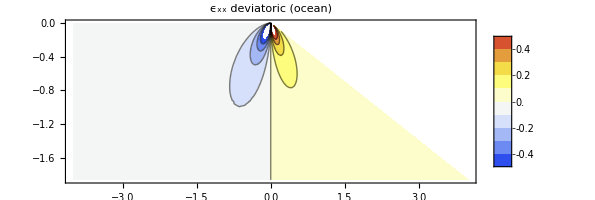

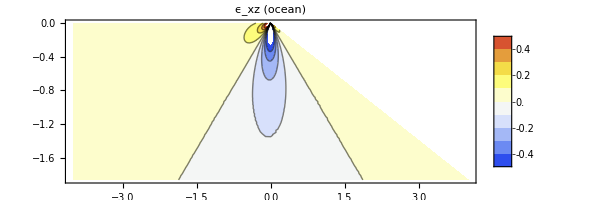

```mathematica
solplot=ReplaceAll[solocean,{δ->δval}];
Aval=A/.solplot[[1]];
Bval=B/.solplot[[1]];
Cval=C/.solplot[[1]];
Dval=D/.solplot[[1]];
toplotxx=ReplaceAll[edotxxdev,{A->Aval,B->Bval,C->Cval,D->Dval}]//FullSimplify;
toplotxz=ReplaceAll[edotxz,{A->Aval,B->Bval,C->Cval,D->Dval}]//FullSimplify;
ContourPlot[toplotxx,{x,-4,4},{z,-4*Tan[δval],0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},z+Tan[δval]*x<=0],AspectRatio->Automatic,PlotRange->{-0.5,0.5},PlotLabel->"ϵ_xx deviatoric (ocean)"]
ContourPlot[toplotxz,{x,-4,4},{z,-4*Tan[δval],0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},z+Tan[δval]*x<=0],AspectRatio->Automatic,PlotRange->{-0.5,0.5},PlotLabel->"ϵ_xz (ocean)"]
```

# Convert to MATLAB expressions

```mathematica
PrintMatlab[ReplaceAll[vx,{δ->dip}],"vx"]
PrintMatlab[ReplaceAll[vz,{δ->dip}],"vz"]
PrintMatlab[ReplaceAll[solarc,{δ->dip}],"constants_arc"]
PrintMatlab[ReplaceAll[solocean,{δ->dip}],"constants_ocean"]
```

vx=(-1).*B+(-1).*x.*(C.*x+D.*z).*(x.^2+z.^2).^(-1)+(-1).*D.* ...
  atan2(z, x);

vz=A+(-1).*z.*(C.*x+D.*z).*(x.^2+z.^2).^(-1)+C.*atan2(z, x);

constants_arc=[0,(-1).*(2.*cos(dip)+(-2).*cos(dip).*cos(2.*dip)+(-4).* ...
  dip.*sin(dip)+(-2).*sin(dip).*sin(2.*dip)).*(1+(-4).*dip.^2+ ...
  (-2).*cos(2.*dip)+cos(2.*dip).^2+sin(2.*dip).^2).^(-1),(2.* ...
  cos(dip)+(-2).*cos(dip).*cos(2.*dip)+(-4).*dip.*sin(dip)+( ...
  -2).*sin(dip).*sin(2.*dip)).*(1+(-4).*dip.^2+(-2).*cos(2.* ...
  dip)+cos(2.*dip).^2+sin(2.*dip).^2).^(-1),(2.*dip.*csc((1/2) ...
  .*dip+(-1/4).*pi).^2.*csc((1/2).*dip+(1/4).*pi).^2+csc((1/2) ...
  .*dip+(-1/4).*pi).^2.*csc((1/2).*dip+(1/4).*pi).^2.*sin(2.* ...
  dip)).^(-1).*(2.*cos(dip).*csc((1/2).*dip+(-1/4).*pi).^2.* ...
  csc((1/2).*dip+(1/4).*pi).^2+(-1).*csc((1/2).*dip+(-1/4).* ...
  pi).^2.*csc((1/2).*dip+(1/4).*pi).^2.*(2.*cos(dip)+(-2).* ...
  cos(dip).*cos(2.*dip)+(-4).*dip.*sin(dip)+(-2).*sin(dip).* ...
  sin(2.*dip)).*(1+(-4).*dip.^2+(-2).*cos(2.*dip)+cos(2.*dip) ...
  .^2+sin(2.*dip).^2).^(-1)+cos(2.*dip).*csc((1/2).*dip+(-1/4) ...
  .*pi).^2.*csc((1/2).*dip+(1/4).*pi).^2.*(2.*cos(dip)+(-2).* ...
  cos(dip).*cos(2.*dip)+(-4).*dip.*sin(dip)+(-2).*sin(dip).* ...
  sin(2.*dip)).*(1+(-4).*dip.^2+(-2).*cos(2.*dip)+cos(2.*dip) ...
  .^2+sin(2.*dip).^2).^(-1))];

constants_ocean=[pi.*(2+(-2).*cos(dip)+(-2).*cos(2.*dip)+2.*cos(dip).*cos( ...
  2.*dip)+4.*dip.*sin(dip)+(-4).*pi.*sin(dip)+2.*sin(dip).* ...
  sin(2.*dip)).*((-1)+4.*dip.^2+(-8).*dip.*pi+4.*pi.^2+2.*cos( ...
  2.*dip)+(-1).*cos(2.*dip).^2+(-1).*sin(2.*dip).^2).^(-1),( ...
  -1)+(-1).*(2+(-2).*cos(dip)+(-2).*cos(2.*dip)+2.*cos(dip).* ...
  cos(2.*dip)+4.*dip.*sin(dip)+(-4).*pi.*sin(dip)+2.*sin(dip) ...
  .*sin(2.*dip)).*((-1)+4.*dip.^2+(-8).*dip.*pi+4.*pi.^2+2.* ...
  cos(2.*dip)+(-1).*cos(2.*dip).^2+(-1).*sin(2.*dip).^2).^(-1) ...
  +pi.*((-2).*dip.*csc((1/2).*dip+(-1/4).*pi).^2.*csc((1/2).* ...
  dip+(1/4).*pi).^2+2.*pi.*csc((1/2).*dip+(-1/4).*pi).^2.*csc( ...
  (1/2).*dip+(1/4).*pi).^2+(-1).*csc((1/2).*dip+(-1/4).*pi) ...
  .^2.*csc((1/2).*dip+(1/4).*pi).^2.*sin(2.*dip)).^(-1).*(2.* ...
  csc((1/2).*dip+(-1/4).*pi).^2.*csc((1/2).*dip+(1/4).*pi).^2+ ...
  (-2).*cos(dip).*csc((1/2).*dip+(-1/4).*pi).^2.*csc((1/2).* ...
  dip+(1/4).*pi).^2+csc((1/2).*dip+(-1/4).*pi).^2.*csc((1/2).* ...
  dip+(1/4).*pi).^2.*(2+(-2).*cos(dip)+(-2).*cos(2.*dip)+2.* ...
  cos(dip).*cos(2.*dip)+4.*dip.*sin(dip)+(-4).*pi.*sin(dip)+ ...
  2.*sin(dip).*sin(2.*dip)).*((-1)+4.*dip.^2+(-8).*dip.*pi+4.* ...
  pi.^2+2.*cos(2.*dip)+(-1).*cos(2.*dip).^2+(-1).*sin(2.*dip) ...
  .^2).^(-1)+(-1).*cos(2.*dip).*csc((1/2).*dip+(-1/4).*pi) ...
  .^2.*csc((1/2).*dip+(1/4).*pi).^2.*(2+(-2).*cos(dip)+(-2).* ...
  cos(2.*dip)+2.*cos(dip).*cos(2.*dip)+4.*dip.*sin(dip)+(-4).* ...
  pi.*sin(dip)+2.*sin(dip).*sin(2.*dip)).*((-1)+4.*dip.^2+(-8) ...
  .*dip.*pi+4.*pi.^2+2.*cos(2.*dip)+(-1).*cos(2.*dip).^2+(-1) ...
  .*sin(2.*dip).^2).^(-1)),(2+(-2).*cos(dip)+(-2).*cos(2.*dip) ...
  +2.*cos(dip).*cos(2.*dip)+4.*dip.*sin(dip)+(-4).*pi.*sin( ...
  dip)+2.*sin(dip).*sin(2.*dip)).*((-1)+4.*dip.^2+(-8).*dip.* ...
  pi+4.*pi.^2+2.*cos(2.*dip)+(-1).*cos(2.*dip).^2+(-1).*sin( ...
  2.*dip).^2).^(-1),((-2).*dip.*csc((1/2).*dip+(-1/4).*pi) ...
  .^2.*csc((1/2).*dip+(1/4).*pi).^2+2.*pi.*csc((1/2).*dip+( ...
  -1/4).*pi).^2.*csc((1/2).*dip+(1/4).*pi).^2+(-1).*csc((1/2) ...
  .*dip+(-1/4).*pi).^2.*csc((1/2).*dip+(1/4).*pi).^2.*sin(2.* ...
  dip)).^(-1).*(2.*csc((1/2).*dip+(-1/4).*pi).^2.*csc((1/2).* ...
  dip+(1/4).*pi).^2+(-2).*cos(dip).*csc((1/2).*dip+(-1/4).*pi) ...
  .^2.*csc((1/2).*dip+(1/4).*pi).^2+csc((1/2).*dip+(-1/4).*pi) ...
  .^2.*csc((1/2).*dip+(1/4).*pi).^2.*(2+(-2).*cos(dip)+(-2).* ...
  cos(2.*dip)+2.*cos(dip).*cos(2.*dip)+4.*dip.*sin(dip)+(-4).* ...
  pi.*sin(dip)+2.*sin(dip).*sin(2.*dip)).*((-1)+4.*dip.^2+(-8) ...
  .*dip.*pi+4.*pi.^2+2.*cos(2.*dip)+(-1).*cos(2.*dip).^2+(-1) ...
  .*sin(2.*dip).^2).^(-1)+(-1).*cos(2.*dip).*csc((1/2).*dip+( ...
  -1/4).*pi).^2.*csc((1/2).*dip+(1/4).*pi).^2.*(2+(-2).*cos( ...
  dip)+(-2).*cos(2.*dip)+2.*cos(dip).*cos(2.*dip)+4.*dip.*sin( ...
  dip)+(-4).*pi.*sin(dip)+2.*sin(dip).*sin(2.*dip)).*((-1)+4.* ...
  dip.^2+(-8).*dip.*pi+4.*pi.^2+2.*cos(2.*dip)+(-1).*cos(2.* ...
  dip).^2+(-1).*sin(2.*dip).^2).^(-1))];